```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Get["PlotStyles.m"]
```

/Users/yorickreum/PycharmProjects/pytorch_pde/approximator/examples/richards/results-thesis/hyperstudy-analysis

```mathematica
Get["https://raw.githubusercontent.com/mark-caprio/CustomTicks/master/CustomTicks.m"]
```

```mathematica
OverleafPath = "/Users/yorickreum/Dropbox/Apps/Overleaf/BA Thesis (MIT Template)"
```

/Users/yorickreum/Dropbox/Apps/Overleaf/BA Thesis (MIT Template)

```mathematica
(* dataRaw = Import["study_1598064702.csv", "Dataset", HeaderLines-> 1] *)
dataRaw = Import["study_1616215167_t_1616246939.2514968.csv", "Dataset", HeaderLines -> 1]
```

```mathematica
data = dataRaw[Select[(#"state" == "COMPLETE")&] , All][Select[(DateObject[#"datetime_complete"]- DateObject[#"datetime_start"]) > Quantity[1, "Minutes"]&],All][All, 
<|"Number" -> #"number", 
"Duration" -> QuantityMagnitude[
DateDifference[DateObject[#"datetime_start"],DateObject[#"datetime_complete"] ], "Seconds"],
"Hidden layers" -> #"params_n_hidden_layers",
"Neurons per layer" -> #"params_n_neurons_per_layer",
"Value" -> #"value"
|>&
]
```

```mathematica
data[SortBy["Value"],All]
First@%
bestChoice = Normal@Values@%[{"Hidden layers", "Neurons per layer"}]
```

{9,36}

{9,36}

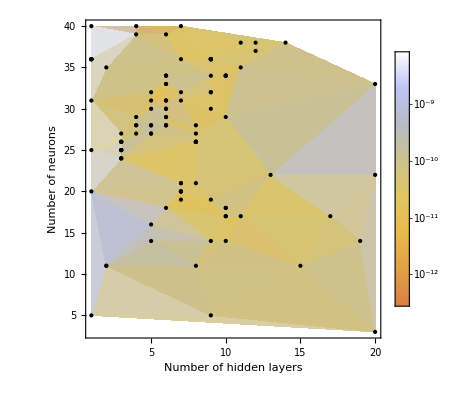

/Users/yorickreum/Dropbox/Apps/Overleaf/BA Thesis (MIT Template)/assets/figs/Evaluation/Celia/Hyperparameters-Min.pdf

```mathematica
ptsPlt = Normal@Values@data[All, {"Hidden layers", "Neurons per layer", "Value"}];
First@SortBy[%, #[[3]]&];
bestPts = %[[1;;2]]
pltHyperparams = Show[
ListDensityPlot[
ptsPlt,
ClippingStyle->Automatic,
Mesh->Full,
Epilog->{
Style[Point[(#[[{1,2}]]&/@ ptsPlt)],Directive[Black]],
Style[Point[bestPts],Directive[Green]]
},
Mesh-> Full,
PlotTheme->"Detailed",
ScalingFunctions->"Log",
PlotRangePadding->Scaled[.01],
ColorFunction->"BeachColors",
PlotLegends->Placed[
BarLegend[Automatic,
LegendMarkerSize->340,
LegendMargins->{{10,0},{0,0}}],
Right]
],
FrameLabel-> {"Number of hidden layers","Number of neurons"},
FrameStyle-> Directive[Black,13],
FrameTicks->{{LinTicks[1,40],None},{LinTicks[1,21],None}}
]
Export[FileNameJoin[{OverleafPath, "assets/figs/Evaluation/Celia/Hyperparameters-Min.pdf"}], pltHyperparams]
```

```mathematica
dataMedianized=<|"Hidden layers" -> #[[1]],"Neurons per layer" -> #[[2]],"Median value" -> #[[3]]|>& /@ data[ GroupBy["Hidden layers"],GroupBy["Neurons per layer"]][All,All,Merge[Median]][All,All,"Value"][AssociationSerialize]
```

{4,40}

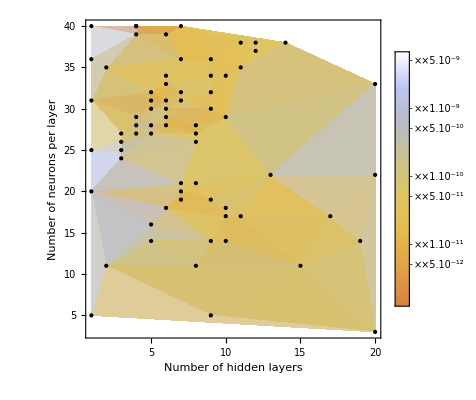

/Users/yorickreum/Dropbox/Apps/Overleaf/BA Thesis (MIT Template)/assets/figs/Evaluation/Celia/Hyperparameters-Median.pdf

```mathematica
ptsPlt = Normal@Values@dataMedianized[All, {"Hidden layers", "Neurons per layer", "Median value"}];
First@SortBy[%, #[[3]]&];
bestPts = %[[1;;2]]
pltHyperparams = Show[
ListDensityPlot[
ptsPlt,
PlotRange->Full,
ClippingStyle->Automatic,
Mesh->Full,
Epilog->{
Style[Point[(#[[{1,2}]]&/@ ptsPlt)],Directive[Black]],
Style[Point[bestPts],Directive[Green]]
},
Mesh-> Full,
PlotTheme->"Detailed",
ScalingFunctions->"Log",
PlotRangePadding->Scaled[.01],
ColorFunction->"BeachColors",
PlotLegends->Placed[
BarLegend[Automatic,
LegendMarkerSize->340,
LegendMargins->{{10,0},{0,0}}],
Right]
],
FrameLabel-> {"Number of hidden layers","Number of neurons per layer"},
FrameStyle-> Directive[Black,13],
FrameTicks->{{LinTicks[1,40],None},{LinTicks[1,21],None}}
]
Export[FileNameJoin[{OverleafPath, "assets/figs/Evaluation/Celia/Hyperparameters-Median.pdf"}], pltHyperparams]
```

```mathematica
Length@data
```

111

```mathematica
Length@dataMedianized
```

69